1000

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.502351 | 0.0535275 | 9.38492 | 1.67317×10^-9
b | 16.254 | 0.0849085 | 191.43 | 9.96132×10^-40

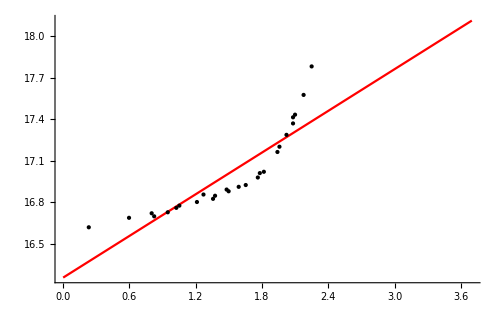

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["noyola.dat"];
L=Length[data];
Ie=1000
(*Ref = 12*)
Ip[R_]:=a*R+b
(*Plot[Log[Ip[R]],{R,0,12}]*)
fit = NonlinearModelFit[data,Ip[R],{a,b},R,MaxIterations->1000];
(*fit["BestFit"]*)
fit["ParameterTable"]
Plot[fit[R],{R,0,3.7},PlotStyle->Red,Epilog:>Point[data],ImageSize->500]
```